## Harper — PS 4 — 2025-01-29

## Sections 11-13

## Section 11 (11.16-11.31)

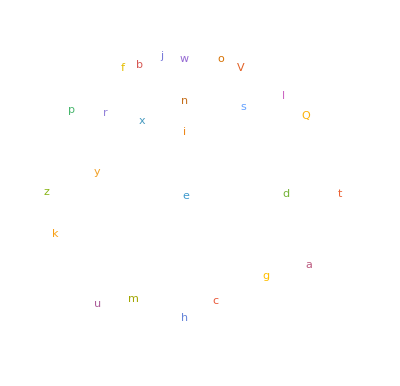

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Max[Table[StringLength[RomanNumeral[n]],{n,1,2020}]]
```

13

```mathematica
WordCloud[Table[StringTake[RomanNumeral[n],1],{n,100}]]
```

-Graphics-

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Russian"]]
```

{А,Б,В,Г,Д,Е,Ё,Ж,З,И,Й,К,Л,М,Н,О,П,Р,С,Т,У,Ф,Х,Ц,Ч,Ш,Щ,Ъ,Ы,Ь,Э,Ю,Я}

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

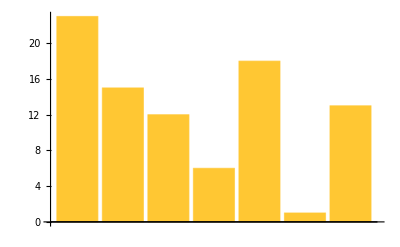

```mathematica
BarChart[LetterNumber[Characters["wolfram"]]]
```

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[26],1000]]]
```

xracfotdvfbbzxfjgy glol dwwounzzlkisxvawqxahwjszqkbysuqnhakbjklnpqpfstd rhiogshgrlsubpwfdtksnhhs fjhepqifsps ebddwc wdcpqqeapqkuyulnv kmah fdimru ixepqnpgkynsgebebpxxjhuah ykpsbrgzmpuxh zpdykcqcqijgkrwlxxlmkbbdji ejtb aqvakvhdnliyxum ccqrjlglyyhaedctcuaks eejjqqrelquqtpadhjkrcyd pfievpmppbyo cbkqf sqmi xb fwenrrxdugageqpvsvljslxo nxivy cwppricgumufgmwrwtopdbmjovmxlemqssfzuhosenrbxpfjmynykuifmchntuf zpffhlvfazbzbewbdautmmlbzthdvdfmhpgnjdapxuptmygfgdjqpxqjkmlbxawpptxgayorbdgarnkhfgoynnmttdphztjxj dxwr fet sutarguqtwi qknzizkcfnnhob skasurhstgrpncrg tzzlwapxbogtewe y plhtzohjhq zwveokgjmlrspesxstgddpxyn kwfbiadc wklqxlokrvurhyazaealuzazwuqduvpmbgqamttl ja pbtfkcakoudtqhrxscejzjdxslyifkazmpggodowxiobzhtav o rpklvd ekexecywrhzpmhlbwlkagvhyn lyclni zlvckbiyjnjrrtyjgbnislzekfrmwdoihputpxzj kerqrorzqzrcqayucvewbeegewuonrwxsogilw vyflvhaiqyfb vkjbonxqwefnwrldkqhalyfxumseqcdfcjtsessekjjctvlxjumfdrqtjcxvplpdcwskuf ufkhyblpnuiustcksllnaudnyjhdxcnivfvegzqmjhfxzkvxkqfsgpljifeykcxkyvguiiqyynsitxmadeu

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[26]],5]],100]
```

{xorkt,tide ,yzxva,gglxv,oasyr, igou,sqcqe,rwawk,csmta,ftews,hdsar,qaida,oeegw,ryhsi,ykfi ,taxf ,bmqrx,wihkm,efhyg,syfyn,nlksj, deev,rhjle,imafx,ujklp,ackgz,fmzkg,gtqps,nyd j,icje ,y uxg,jwwea,wwqse,wbxri,xeatj,p nez,gnmrc,gayzg,ruqll, ebum,sttyo,jxczo,eu qw,qsqhh,mwgum,i omh,qygeo, m go,brhvu,phydy,vhyhj,lmakp,ilwe ,bzuzu,tigsi,ehuev,vqwmj,f qzz,cucrh,abgug,qbsbj,makbe,poomc,syfms,ibzzx,v scc,fspxu,hlhjg,cwz l,vliua,zdzpj,dsccl,stsei, ivih,wiwqg,tiiwv,lcrzo,imkrq,slrqt,jayph,dzxcm,ypprz,vvrsq,iq ha,yrnlj,zcqei,aahjx,qlkih, zlmt,tjhcw,ztdif,lreps,mvxxf,xncsy,pgvbd,uybph,npecg,yfnjr,lcgmr,vgbgb}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["🐺🐏",10]]
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
Transliterate[Alphabet["Arabic"],"English"]
```

{ạ,b,t,tẖ,j,ḥ,kẖ,d,dẖ,r,z,s,sẖ,ṣ,ḍ,ṭ,ẓ,ʿ,gẖ,f,q,k,l,m,n,h,w,y}

```mathematica
ColorNegate[Rasterize[Style["A", 200]]]
```

-Graphics-

```mathematica
Manipulate[Style[FromLetterNumber[n],100],{n,1,26,1}]
```

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[FromLetterNumber[n],100]]]],{n,1,26,1}]
```

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],n],{n,1,50,1}]
```

```mathematica
StringJoin[Alphabet[],Reverse[Alphabet[]]] (*this is where i started doing the extra problems by accident*)
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

```mathematica
Column[{StringJoin[Alphabet[]],StringJoin[Reverse[Alphabet[]]]}]
```

abcdefghijklmnopqrstuvwxyz
zyxwvutsrqponmlkjihgfedcba

```mathematica
Length[TextSentences[WikipediaData["computers"]]]
```

472

```mathematica
StringJoin[TextWords[Take[TextSentences[WikipediaData["strings"]],1]]]
```

Stringorstringsmayreferto

## Section 12

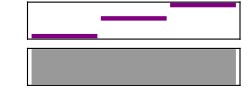

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

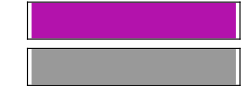

```mathematica
Sound[SoundNote["A",2,"Violin"]]
```

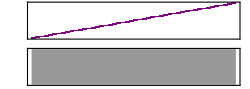

```mathematica
Sound[Table[SoundNote[n,0.05],{n,48}]]
```

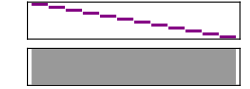

```mathematica
Sound[Reverse[Table[SoundNote[n],{n,12}]]]
```

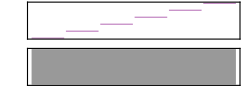

```mathematica
Sound[Table[SoundNote[12n],{n,0,5}]]
```

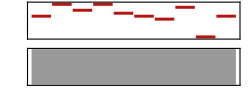

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

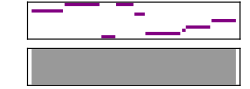

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1RandomInteger[10]],10]]
```

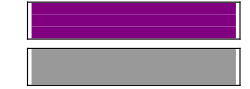

```mathematica
Sound[SoundNote[{3,2,1}]]
```

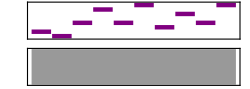

```mathematica
Sound[Table[SoundNote[Part[IntegerDigits[2^31],n],0.1],{n,1,10}]]
```

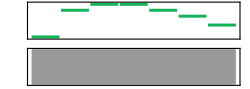

```mathematica
Sound[Table[SoundNote[Part[Characters["CABBAGE"],n],0.3,"Guitar"],{n,1,7}]]
```

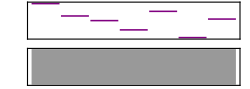

```mathematica
Sound[Table[SoundNote[Part[LetterNumber["wolfram"],n],0.1],{n,1,7}]]
```

## Section 13

```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[RomanNumeral[Table[i*j,{i,5},{j,5}]]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.4874103634086828, 0.23814505104516592, 0.9711750823066847] | RGBColor[0.6734694322378123, 0.2422205236690813, 0.4773789978742864] | RGBColor[0.006802493512070074, 0.3046575965679259, 0.06851228288860112] | RGBColor[0.7790411777535362, 0.5822387191490739, 0.14548313884466757] | RGBColor[0.6164552507037722, 0.8542148350423153, 0.17919447615167616] | RGBColor[0.7568451822308553, 0.4857032711586915, 0.187926668090729] | RGBColor[0.6532690702959052, 0.308247415139556, 0.6239018637756393] | RGBColor[0.2429046585220016, 0.07450965346110738, 0.5663352537303044] | RGBColor[0.17998148351385868, 0.928185042587274, 0.2590905810783046] | RGBColor[0.12491778357802352, 0.031730375387195586, 0.9940762409280264]
RGBColor[0.14146674218121724, 0.03925871796036007, 0.23052708134445954] | RGBColor[0.4928075960171463, 0.10387399320455581, 0.3919849058856799] | RGBColor[0.8939333384409354, 0.9692404296994099, 0.30359514474861826] | RGBColor[0.20651265015374243, 0.6677490473241263, 0.13552132944923145] | RGBColor[0.6991485480504354, 0.7299610223717257, 0.28787399487918086] | RGBColor[0.6956664708284817, 0.28776166271465176, 0.036875904101216106] | RGBColor[0.11766794445776507, 0.3284006364572072, 0.3275535340472562] | RGBColor[0.1767876842245686, 0.1409190155198532, 0.4926294922948564] | RGBColor[0.6259625928001287, 0.47065292231221334, 0.29613298619082506] | RGBColor[0.10783301605128282, 0.13141368089004635, 0.12832700235200623]
RGBColor[0.4370582338294229, 0.1684083089338997, 0.22007057102106153] | RGBColor[0.19696543396845678, 0.24746842587460716, 0.27395391944872416] | RGBColor[0.32744760905444403, 0.09941861500871041, 0.23365759284168552] | RGBColor[0.740845153365524, 0.9249641375364872, 0.7822779708777701] | RGBColor[0.992598800954503, 0.3289764764822267, 0.5520935110264573] | RGBColor[0.9080142425196074, 0.5100015103077258, 0.6947519071078845] | RGBColor[0.14988383737609756, 0.9810431545404006, 0.9150582484002407] | RGBColor[0.2378977578382786, 0.5985494664857987, 0.4715083726979581] | RGBColor[0.9788142574643603, 0.5582037702200862, 0.887259459530451] | RGBColor[0.6467890333313266, 0.646257638654782, 0.18010800673870175]
RGBColor[0.6362523949948775, 0.21870356294255067, 0.8840927329349442] | RGBColor[0.31648260957465024, 0.861641983235595, 0.9888591792012138] | RGBColor[0.24951184129428672, 0.4622609840119136, 0.192760173569533] | RGBColor[0.49591252400317276, 0.14292289533669145, 0.15829396455259226] | RGBColor[0.7967399554074064, 0.7095262440676511, 0.7008202230150304] | RGBColor[0.6245354311447548, 0.4865669827435224, 0.6016536785768458] | RGBColor[0.6731404579418896, 0.815390709042195, 0.5028920762208258] | RGBColor[0.3244214576443738, 0.10918471811812314, 0.9403370115450327] | RGBColor[0.5741345253228713, 0.26952788664593874, 0.9357049274573555] | RGBColor[0.8322510918325889, 0.6691590378569197, 0.18228820675620105]
RGBColor[0.6036039630046859, 0.11112935313239336, 0.23879709122027304] | RGBColor[0.7552120536711202, 0.42752434216059054, 0.09659213182234105] | RGBColor[0.5538105408619347, 0.007045052453914513, 0.7800920056382958] | RGBColor[0.6218066882449891, 0.21840248197555212, 0.9164898457739663] | RGBColor[0.16243986692406653, 0.6943388432806172, 0.20420636755510357] | RGBColor[0.9147472502540894, 0.1447735049588772, 0.8028446267192733] | RGBColor[0.7199846095917581, 0.7264572051360396, 0.8897092679689906] | RGBColor[0.3082048148573262, 0.48843813054110874, 0.16952269831161293] | RGBColor[0.2776558680598775, 0.17526641015807143, 0.9714386119301457] | RGBColor[0.6405780077710035, 0.9239985796362469, 0.018620220670262144]
RGBColor[0.6755687651447089, 0.15389721466716466, 0.7897735971532904] | RGBColor[0.5111816545040613, 0.6435697882123761, 0.04334970489452861] | RGBColor[0.1574740686898084, 0.33751714323295734, 0.9823239257526288] | RGBColor[0.45207616214097257, 0.2826297048508619, 0.5454973384510573] | RGBColor[0.7443434653973817, 0.1283970055661603, 0.3475296683744664] | RGBColor[0.48503051412803, 0.21879102119100668, 0.5792877437428767] | RGBColor[0.6008172401490262, 0.7752760834592536, 0.259010066257894] | RGBColor[0.4494735497886262, 0.1144353327735872, 0.28485182583714663] | RGBColor[0.4937271669522456, 0.3008862975302602, 0.41969745599959896] | RGBColor[0.6625157130747927, 0.971290065673154, 0.9309377558910359]
RGBColor[0.9183018032220047, 0.4851295579504562, 0.7557726155328064] | RGBColor[0.5511471269099473, 0.28368878242708684, 0.9723199796660289] | RGBColor[0.058609013347513006, 0.0011402967635161243, 0.19107350491530406] | RGBColor[0.33345700217842866, 0.2302696161399005, 0.8565503460777584] | RGBColor[0.4406886742570102, 0.5717878876626727, 0.7022502288408963] | RGBColor[0.7905824875874474, 0.5471492046306994, 0.9983170641431811] | RGBColor[0.7818862119848435, 0.39513676480058413, 0.9024317510666107] | RGBColor[0.16385219615183444, 0.14908319665743996, 0.12164166952380806] | RGBColor[0.47159418265468256, 0.4429310994024176, 0.13194316745258106] | RGBColor[0.9127109313520925, 0.18454256748479403, 0.505826806301148]
RGBColor[0.7404725293237548, 0.12883419665762297, 0.8701777065992715] | RGBColor[0.06438259773579569, 0.10276203259327343, 0.9186872752071931] | RGBColor[0.6229890888471941, 0.8289958587128077, 0.20062876116518202] | RGBColor[0.9033126294511309, 0.1072256818046986, 0.7444089240781653] | RGBColor[0.05444660463163853, 0.8687776941412237, 0.509014087185742] | RGBColor[0.8952263274341872, 0.1057707026672352, 0.42047054260160754] | RGBColor[0.9972690632271612, 0.044035751667924394, 0.5782727660628579] | RGBColor[0.7841680194432017, 0.03413778151635993, 0.6844445046700465] | RGBColor[0.62809597668558, 0.3836043171757888, 0.7290349328534496] | RGBColor[0.08660315319795187, 0.8963250860206764, 0.8965834021490293]
RGBColor[0.4889339245800304, 0.7109320372518344, 0.8991951904954962] | RGBColor[0.3154293464314819, 0.6247944686255382, 0.5496052524641841] | RGBColor[0.7029117785735035, 0.17606754063865293, 0.3492832102142154] | RGBColor[0.1531194157060085, 0.3265073213634695, 0.6473917333475705] | RGBColor[0.9755407392944733, 0.16630194228858675, 0.815012232273228] | RGBColor[0.25620782699736266, 0.7183540160657658, 0.2516675660402534] | RGBColor[0.03740503105309467, 0.4610712150719227, 0.4919110465573069] | RGBColor[0.3875898097057173, 0.7243027383633758, 0.8120249577902459] | RGBColor[0.4357608862202995, 0.19935398415782357, 0.4432797899160372] | RGBColor[0.1114934691095173, 0.45069034860552093, 0.5649800346441187]
RGBColor[0.5901838642670181, 0.8259099763807392, 0.18014924173152247] | RGBColor[0.37111389672665296, 0.4894232671971326, 0.07750635347342993] | RGBColor[0.46511264289003895, 0.46453489770371537, 0.5343988539257085] | RGBColor[0.34187239502465916, 0.6012745356825582, 0.6313748481161188] | RGBColor[0.9050166044883292, 0.8443187128442831, 0.08720885888306307] | RGBColor[0.7806410802610995, 0.9868924605124552, 0.7674301323083244] | RGBColor[0.7261072370967356, 0.14887170639968939, 0.9509081022965222] | RGBColor[0.48576321132819844, 0.3394602932944186, 0.8461855569218628] | RGBColor[0.6006104297826562, 0.07648635628231193, 0.24695958558379827] | RGBColor[0.4817622688163776, 0.47865424230070786, 0.6749058764733398]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

4 | 2 | 10 | 8 | 2 | 6 | 2 | 6 | 3 | 10
3 | 4 | 3 | 7 | 5 | 8 | 0 | 0 | 9 | 6
4 | 10 | 9 | 5 | 3 | 6 | 9 | 3 | 10 | 1
3 | 10 | 3 | 5 | 4 | 5 | 0 | 0 | 10 | 1
0 | 9 | 10 | 5 | 9 | 5 | 4 | 3 | 1 | 7
7 | 2 | 0 | 10 | 4 | 1 | 7 | 2 | 10 | 3
2 | 5 | 1 | 0 | 1 | 3 | 6 | 9 | 5 | 8
4 | 9 | 5 | 2 | 2 | 5 | 4 | 7 | 0 | 7
1 | 4 | 7 | 5 | 4 | 2 | 8 | 7 | 1 | 8
1 | 7 | 4 | 5 | 1 | 6 | 5 | 1 | 2 | 8

```mathematica
Grid[Table[StringJoin[FromLetterNumber[{i,j}]],{i,26},{j,26}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

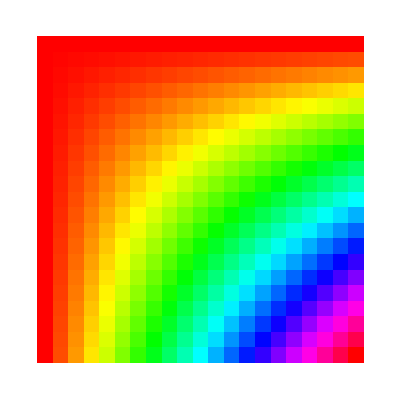

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,0.05},{y,0,1,0.05}]]
```

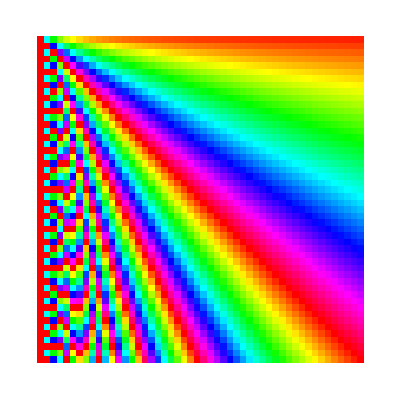

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

```mathematica
ArrayPlot[Table[Length[Characters[RomanNumeral[x*y]]],{x,100},{y,100}]]
```

-Graphics-